# Метод на хордите

Задача: Дадено е уравенението:
(√(x^3) - (1 + p + q) * sin(x))/(1 + cos^2(x)), където p и q са съответно предпоследната и последната цифра от факултетния ни номер (в случая p = 1 а q = 9)
(√(x^3) - 11* sin(x))/(1 + cos^2(x))
	 1.  Да се намери общия брой на корените на уравнението.
2. Да се локализира най-малкия реален корен в интервала [a, b]. 
3. Да се проверят условията за приложение на метода на хордите.
	         - проверка на сходимост
		- избор на начално приближение и постоянна точка
		- итерациите
	 4.  Да се изчисли корена по метода на хордите с точност 0,000001. Представете таблица с изчисленията.
	 5.  Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
6.  Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := (√(x^3)-11)/(2 - Sin[x])
```

```mathematica
f[x]
```

(-11+√(x^3))/(2-Sin[x])

## 1. Да се намери общия брой на корените на уравнението

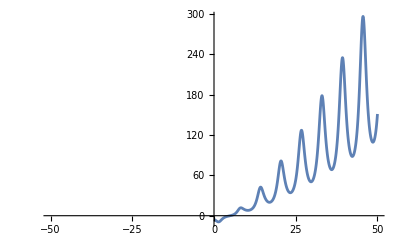

```mathematica
Plot[f[x], {x, -50, 50}]
```

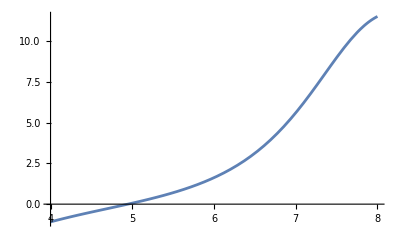

```mathematica
Plot[f[x], {x, 4, 8}]
```

Брой корени: 1

## 2. Да се локализира най-малкия реален корен в интервала [a, b]

```mathematica
Plot[f[x], {x, 4, 8}]
```

-Graphics-

```mathematica
f[4.]
```

-1.08822

```mathematica
f[8.]
```

11.505

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции.
(2) f(5) = -1.088 ... < 0
       f(7) = 11.505 ... > 0
       => Функцията има различни знаци в двата края на разглеждания интервал [4; 8].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [4; 8].

## 3. Да се проверят условията за приложение на метода на хордите

### Проверка на сходимост

#### Графика на първата производна

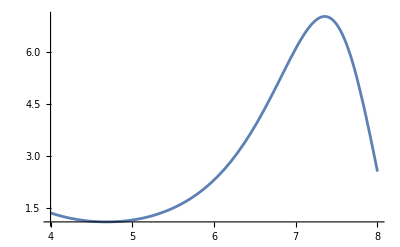

```mathematica
Plot[f'[x],{x,4,8}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [4; 8] са между 1 и 7.1 Следователно първата f'(x) > 0 в целия разглеждан интервал [4; 8].

#### Графика на втората производна

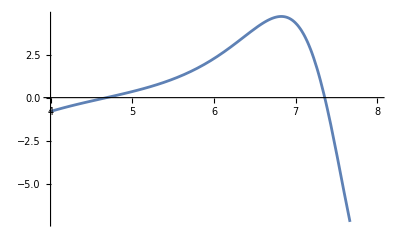

```mathematica
Plot[f''[x],{x,4,8}]
```

Извод : (2) Стойностите на втората производна в разглеждания интервал [4; 8] са между 1 и -8. Следователно втората производна няма постоянна стойност в разглеждания интервал [4, 8] .